# Particle on the Innermost Stable Circular Orbit of a Rapidly Spinning Black Hole [Phys. Rev. D 92, 064029 (2015)]

## Sam Gralla, Achilleas Porfryiadias and Niels Warburton

This notebook computes the radiation emitted by a particle on the innermost stable circular orbit of a rapidly spinning black hole analytically, working to leading order in the deviation from extremality. We give the formula for both a scalar and gravitational particle.

Please cite Phys. Rev. D 92, 064029 (2015), arXiv:1506.08496 if you use the flux formulae in your work

Load the SpinWeightedSpheroidalHarmonics package from the Black Hole Perturbation Toolkit (freely available at https://bhptoolkit.org/)

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

## Formula for the scalar case (s=0)

```mathematica
Γ[θ_]:=Gamma[θ];
Kl[l_,m_]:=SpheroidalEigenvalue[l,m,I m/2];
h0[l_,m_]:=1/2+Sqrt[1/4+Kl[l,m]-2 m^2]
S0[l_,m_]:=Sqrt[2π]Sqrt[(2l+1)/(4π)((l-m)!)/((l+m)!)]SpheroidalPS[l,m, I m/2,0]
```

```mathematica
EdotInf[l_,m_]:=Block[{h=h0[l,m],λ=1,M=1,r0=2^(1/3)(ϵ)^(2/3)},λ^2/(24 M^2)S0[l,m]^2 Abs[WhittakerW[I m, h-1/2,3 I m/2]]^2(3 r0/2)^(2 Re[h])m^(4 Re[h]-2)Exp[π m] Abs[((2h-1)Γ[h-I m]^2/Γ[2h]^2)/(1-(3r0/2)^(2h-1)m^(4h-2)(Γ[1-2h]^2/Γ[2h-1]^2 Γ[h-I m]^2/Γ[1-h-I m]^2))]^2
]
```

```mathematica
EdotHoriz[l_,m_]:=Block[{h=h0[l,m],M=1,r0=2^(1/3)ϵ^(2/3),λ=1,α,n,τH,gt,ω,ΩH,Ωϕ,N1},
-λ^2/(16 M^2)r0 Exp[-π m] S0[l,m]^2 Abs[Γ[h-I m]]^2/Abs[Γ[2h]]^2 Abs[WhittakerM[I m, h-1/2,3I m/2]+WhittakerW[I m ,h-1/2,3I m/2] (Γ[1-h-I m]/Γ[1-2h])/((3r0/2)^(1-2h)m^(2-4h)(Γ[2h-1]^2 Γ[1-h-I m]^2)/(Γ[1-2h]^2 Γ[h-I m]^2)-1)]^2
]
```

## Formula for the gravitational case (s=-2)

```mathematica
Γ[θ_]:=Gamma[θ];
K2[l_,m_]:=Block[{s=-2,γ=m/2},SpinWeightedSpheroidalEigenvalue[s,l,m,γ]+2m γ+s(s+1)];
h2[l_,m_]:=1/2+Sqrt[1/4+K2[l,m]-2 m^2]
```

```mathematica
EdotInfG[l_,m_]:=Block[{h=h2[l,m],m0=1,M=1,r0=2^(1/3)ϵ^(2/3),s=-2,S,dS,d2S,γlm,SFunc},
SFunc=SpinWeightedSpheroidalHarmonicS[-2,l,m,N[m/2,40]];
S=Sqrt[2π]SFunc[π/2,0];
dS= Sqrt[2π]Derivative[1,0][SFunc][π/2,0];
d2S=Sqrt[2π]Derivative[2,0][SFunc][π/2,0];

γlm=2((h^2-h+6-I m)S+4(2I+m) dS-4d2S)WhittakerW[I m-2, h-1/2,3 I m/2]+((4+3I m) S-8 I dS)WhittakerW[I m -1,h-1/2,3I m/2];
m0^2/(2^5 3^3 M^2)Abs[γlm]^2(3 r0/2)^(2Re[h])m^(4Re[h]-2)Exp[π m] (Abs[2h-1]^2 Abs[Γ[h+2-I m]]^2 Abs[Γ[h-2-I m]]^2/Abs[Γ[2h]]^4)/(Abs[1-(3 r0/2)^(2h-1)m^(4h-2)Γ[1-2h]^2/Γ[2h-1]^2(Γ[h-I m-s]Γ[h-I m +s])/(Γ[1-h-I m -s] Γ[1-h-I m +s])]^2)
]
```

```mathematica
EdotHorizG[l_,m_]:=Block[{h=h2[l,m],m0=1,M=1,r0=2^(1/3)ϵ^(2/3),s=-2,S,dS,d2S,γlm,δlm,AbsC2,SFunc},
SFunc=SpinWeightedSpheroidalHarmonicS[-2,l,m,N[m/2,40]];
S=Sqrt[2π]SFunc[π/2,0];
dS= Sqrt[2π]Derivative[1,0][SFunc][π/2,0];
d2S=Sqrt[2π]Derivative[2,0][SFunc][π/2,0];

γlm=2((h^2-h+6-I m)S+4(2I+m) dS-4d2S)WhittakerW[I m-2, h-1/2,3 I m/2]+((4+3I m) S-8 I dS)WhittakerW[I m -1,h-1/2,3I m/2];
δlm=2((h^2-h+6-I m)S+4(2I+m)dS-4d2S)WhittakerM[I m -2,h-1/2,3I m/2]-(h-2+I m)((4+3I m)S-8I dS)WhittakerM[I m - 1,h-1/2,3I m/2];
AbsC2=((K2[l,m]-m^2)^2+m^2)((K2[l,m]-m^2-2)^2+9 m^2);
-m0^2/(2^6 3^2 M^2)1/AbsC2 r0 Exp[-π m] Abs[Γ[h-I m -s]]^2/Abs[Γ[2h]]^2 Abs[δlm+γlm (Γ[1-h-I m-s]/Γ[1-2h])/((3 r0/2)^(1-2h)m^(2-4h)Γ[2h-1]^2/Γ[1-2h]^2(Γ[1-h-I m-s]Γ[1-h-I m +s])/(Γ[h-I m -s] Γ[h-I m +s])-1)]^2
]
```

## Numerically evaluate the gravitational fluxes

Numerically evaluate the near-horizon analytic formula to compare with the full numerical (no near-horizon approximation) in Table I of the paper.

```mathematica
res=Table[{N[10^-exp],EdotInfG[2,2],EdotHorizG[2,2],EdotInfG[2,2]/EdotHorizG[2,2]}/.ϵ->10^-exp,{exp,1,13}]
```

{{0.1,0.0265157719758950134395143211692538998,-0.0077938896309991830142389406849618588,-3.4021231030052025284635246784507862},{0.01,0.00571265058151699696160143343379724562,-0.0016791427687248184985489452284240105,-3.402123207102467850875977719711407},{0.001,0.00123075340399398980848589622336412586,-0.00036176037426267247602417014444790493,-3.4021233157513975076715202301082376},{0.0001,0.000265157813800139432981281978772177603,-0.000077938916485267068562548990159542236,-3.4021234289324856626854701436272674},{0.00001,0.0000571265258219004993520865157465444446,-0.000016791431892167658126121820111464768,-3.402123546625412813449678514206742},{1.×10^-6,0.0000123075382947995056199101134381180672,-3.617604617855615422163975387534186×10^-6,-3.4021236688090494386849699827731541},{1.×10^-7,2.65157904257006370944818920410003111×10^-6,-7.7938934676843729145499147073654747×10^-7,-3.4021237954614597912006993715301896},{1.×10^-8,5.71265450457749789378836538747401988×10^-7,-1.6791435667524051303727435271602036×10^-7,-3.4021239265599058355209332423985673},{1.×10^-9,1.23075423787364544805316580953741703×10^-7,-3.6176054000831337920260549374689043×10^-8,-3.4021240620808513295307971908884983},{1.×10^-10,2.65157990983396244709082154229767727×10^-8,-7.7938950855327677064740520866440961×10^-9,-3.402124201999966049410688060573745},{1.×10^-11,5.71265634557326202436238079627170204×10^-9,-1.6791439007217090861882537933293664×10^-9,-3.402124346292130157100339785071485},{1.×10^-12,1.23075462851521588738581430590723662×10^-9,-3.6176060880453425663783837151494418×10^-10,-3.4021244949314387095091567990855328},{1.×10^-13,2.65158073839181547883954609083342782×10^-10,-7.7938964994577357879521757138923421×10^-11,-3.4021246478912063086637944886188755}}

Plot the results (cf. Fig 3)

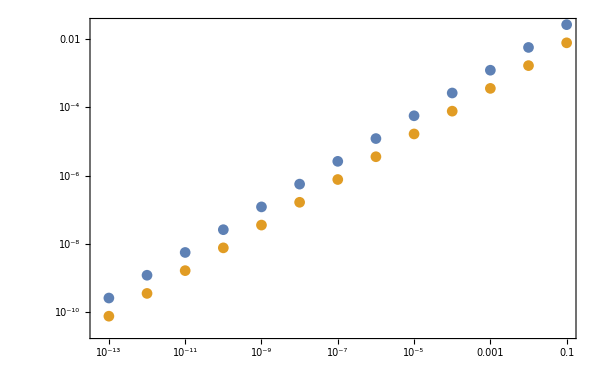

```mathematica
ListLogLogPlot[{res[[All,{1,2}]],Abs[res[[All,{1,3}]]]},PlotTheme->"Detailed",ImageSize->600]
```

Numerically compute the ratio of the ∞ and horizon flux so show the oscillations (see Fig. 4)

```mathematica
res2=Table[{N[10^-exp],EdotInfG[2,2]/EdotHorizG[2,2]}/.ϵ->10^-exp,{exp,5,13,1/10}];
```

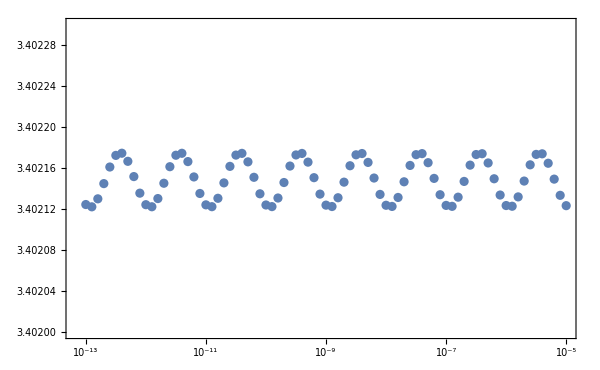

```mathematica
ListLogLinearPlot[{Abs[res2]},PlotTheme->"Detailed",ImageSize->600,PlotRange->{All,{3.402,3.4023}}]
```